```mathematica
(* В данном файле приводится пример построения траекторий траектории полета для точек предыдущего года*)
a = Import[FileNameJoin[{NotebookDirectory[] ,"точки прошлого года.txt"}], "Table"];
R=30;
Rmax=300;

ϕdrop=-1;
ϕNL=-1;
Hpolet=100;
Hud=50;
Hdrop=35;
Ldrop=150;
Lsap=50;

αgr=π/9;
Hgr=1.5;
Lgru=10;
Lgrd=20;



x0=Min[Table[a[[i,1]],{i,1,4}]];
z0=Min[Table[a[[i,2]],{i,1,4}]];
trajectory0=Table[{6378000*(a[[i,1]]-x0)*π/180,Hpolet,6378000*Cos[a[[i,1]]*π/180]*(a[[i,2]]-z0)*π/180,a[[i,3]]},{i,1,Length[a]}];
```

```mathematica
a:=1/(2R);
xmax:=R √(((Rmax/R)^2)^(1/3)-1);
ymax:=-a*xmax^2;
Smax=(2a xmax √(1+4 a^2 xmax^2)+Log[Abs[√(1+4 a^2 xmax^2)+2a xmax]])/(4a);
ϕ0:=ArcTan[2a xmax];
xкп:=xmax*Cos[ϕ0]-ymax*Sin[ϕ0];
yкп:=xmax*Sin[ϕ0]+ymax*Cos[ϕ0];
xo0[ϕ_]:=1/(2a)Tan[ϕ/2-ϕ0]+xmax;
yo0[ϕ_]:=1/(4a)Tan[ϕ/2-ϕ0]^2+ymax;
xo[ϕ_,R_]:=If[Abs[ϕ]<2ϕ0,xo0[ϕ] Cos[ϕ0]-yo0[ϕ] Sin[ϕ0],xкп+R Cos[ϕ0+π/2]];
yo[ϕ_,R_]:=If[Abs[ϕ]<2ϕ0,xo0[ϕ] Sin[ϕ0]+yo0[ϕ] Cos[ϕ0],yкп+R Sin[ϕ0+π/2]];
xb[ϕ_,R_]:=If[ϕ==0,0,2Cos[ϕ/2-ArcTan[yo[ϕ,R]/xo[ϕ,R]]]*√(yo[ϕ,R]^2+xo[ϕ,R]^2)*Cos[ϕ/2]];
yb[ϕ_,R_]:=If[ϕ==0,0,2Cos[ϕ/2-ArcTan[yo[ϕ,R]/xo[ϕ,R]]]*√(yo[ϕ,R]^2+xo[ϕ,R]^2)*Sin[ϕ/2]];
xк[ϕ_,R_,ϕ1_,Rside_]:=xb[ϕ,R] Cos[ϕ1]-If[Rside,-1,1]*yb[ϕ,R] Sin[ϕ1];
yк[ϕ_,R_,ϕ1_,Rside_]:=xb[ϕ,R] Sin[ϕ1]+If[Rside,-1,1]*yb[ϕ,R] Cos[ϕ1];
```

```mathematica
(*----------------------------------------------------------------------------------------------------*)
turn[Δϕ_,x_,y_,ϕ_,Rside_]:=(

Sп={Smax};
xп={0};
yп={0};
ϕп={-ϕ0};
Rп={Rmax};
For[i=2,i<=20,i++,
AppendTo[Sп,Sп[[i-1]]-Smax/19];
AppendTo[xп,xmax/2];
xa=xmax;
xi=0;
Sр=Smax;
While[Abs[Sп[[i]]-Sр]>0.05,
xп[[i]]=(xa+xi)/2;
Sр=1/(4a)(2a xп[[i]] √(1+4 a^2 xп[[i]]^2)+Log[Abs[√(1+4 a^2 xп[[i]]^2)+2a xп[[i]]]]);
If[Sп[[i]]>Sр,xi=xп[[i]],xa=xп[[i]]];
];
AppendTo[yп,a xп[[i]]^2-a xmax^2];
xп[[i]]=-xп[[i]]+xmax;
AppendTo[ϕп,ArcTan[2a (xп[[i]]-xmax)]];
AppendTo[Rп,R(√(((xп[[i]]-xmax)/R)^2+1))^3];
If[Abs[Δϕ/2]<ϕп[[i]]+ϕ0,
xп[[i]]=xo0[Δϕ];
yп[[i]]=yo0[Δϕ];
ϕп[[i]]=ArcTan[2a (xп[[i]]-xmax)];
Rп[[i]]=R(√(((xп[[i]]-xmax)/R)^2+1))^3;
i++;
Break[];
];
];
i--;


For[j=1,j<=i,j++,xd=xп[[j]];yd=yп[[j]];xп[[j]]=Cos[ϕ0]xd-Sin[ϕ0]yd;yп[[j]]=Sin[ϕ0]xd+Cos[ϕ0]yd;ϕп[[j]]=ϕп[[j]]+ϕ0];
k=i;
xт=xп;
yт=yп;
ϕт=ϕп;
Rт=Rп;

del=Round[(Abs[Δϕ]-2ϕ0)/Smax*19*R];
For[j=k+1,j<=k+del,j++,
AppendTo[xт,xo[Δϕ,R]+R*Cos[ϕ0+((j-k)*(Abs[Δϕ]-2ϕ0))/del-π/2]];
AppendTo[yт,yo[Δϕ,R]+R*Sin[ϕ0+((j-k)*(Abs[Δϕ]-2ϕ0))/del-π/2]];
AppendTo[ϕт,ϕ0+((j-k)*(Abs[Δϕ]-2ϕ0))/del];
i++;AppendTo[Rт,R]
];


ϕ02=Δϕ-π;
For[j=k-1,j>=1,j--,xd=xп[[j]];yd=-yп[[j]];AppendTo[xт,Cos[ϕ02]xd-Sin[ϕ02]yd+xb[Δϕ,R]];AppendTo[yт,Sin[ϕ02]xd+Cos[ϕ02]yd+yb[Δϕ,R]];AppendTo[ϕт,-ϕп[[j]]+ϕ02+π];AppendTo[Rт,Rп[[j]]];i++
 ];


For[j=1,j<=i,j++,
xd=xт[[j]];If[Rside,yd=-yт[[j]],yd=yт[[j]]];xт[[j]]=Cos[ϕ]xd-Sin[ϕ]yd+x;yт[[j]]=Sin[ϕ]xd+Cos[ϕ]yd+y;If[Rside,ϕт[[j]]=Mod[-ϕт[[j]]+ϕ,2π];Rт[[j]]=-Rт[[j]],ϕт[[j]]=Mod[ϕт[[j]]+ϕ,2π]]
];

Return[Table[{xт[[j]],yт[[j]],ϕт[[j]],Rт[[j]]},{j,1,Length[xт]}]];

)
```

```mathematica
(*----------------------------------------------------------------------------------------------------*)
Uturn[x1_,y1_,ϕ1_,x2_,y2_]:=(
xц0=x2-x1;
yц0=y2-y1;
xц1=xц0*Cos[ϕ1]+yц0*Sin[ϕ1];
yц1=Abs[-xц0*Sin[ϕ1]+yц0*Cos[ϕ1]];


grE={{0,0}};
maxXgrE=0;
maxJgrE=0;
For[j=0.05,j<=2ϕ0,j=j+0.05,
AppendTo[grE,{xb[j,R],yb[j,R]}];
If[xb[j,R]>maxXgrE,maxXgrE=xb[j,R];maxJgrE=j/0.05+1]
];



xOsave=xo[10π,R];
yOsave=yo[10π,R];
RO=√(xOsave^2+yOsave^2);


If[(xц1-xOsave)^2+(yц1-yOsave)^2>RO^2 || xц1>maxXgrE,Return[False],
For[j=2,j<=maxJgrE,j++,If[grE[[j,1]]>xц0,Break[]]];
If[yц1<(grE[[j,2]]-grE[[j-1,2]])/(grE[[j,1]]-grE[[j-1,1]])*(xц0-grE[[j-1,1]])+grE[[j-1,2]],Return[False],
For[j=Length[grE]-1,j>=maxJgrE,j--,If[grE[[j,1]]>xц0,Break[]]];
If[yц1>(grE[[j+1,2]]-grE[[j,2]])/(grE[[j+1,1]]-grE[[j,1]])*(xц0-grE[[j,1]])+grE[[j,2]],Return[False],Return[True]]
];
];
)
(*----------------------------------------------------------------------------------------------------*)
```

```mathematica
twopointT[x1_,y1_,ϕ1_,x2_,y2_,ϕ2_,l4min_]:=(
xp0=x2-x1;
yp0=y2-y1;
If[ϕ2-ϕ1<=-π,ϕd=2π+ϕ2-ϕ1,If[ϕ2-ϕ1>π,ϕd=-2π+ϕ2-ϕ1,ϕd=ϕ2-ϕ1]];
xp=xp0*Cos[ϕ1]+yp0*Sin[ϕ1]-l4min*Cos[ϕd];
yp=-xp0*Sin[ϕ1]+yp0*Cos[ϕ1]-l4min*Sin[ϕd];

If[Abs[ϕd]<π/18||Abs[ϕd]>(17π)/18,
xpb=xp;ypb=yp;ϕdb=ϕd;
traj1=twopointT[0,0,0,xpb/2,ypb/2,If[Abs[ϕdb]<π/18,If[ypb>=0,(π-ϕdb)/2,-(π+ϕdb)/2],If[ϕdb<0,If[ypb>=0,(2π+ϕdb)/2,ϕdb/2],If[ypb>=0,ϕdb/2,-(2π-ϕdb)/2]]],0];
AppendTo[traj1,{xpb/2,ypb/2,If[Abs[ϕdb]<π/18,If[ypb>=0,(π-ϕdb)/2,-(π+ϕdb)/2],If[ϕdb<0,If[ypb>=0,(2π+ϕdb)/2,ϕdb/2],If[ypb>=0,ϕdb/2,-(2π-ϕdb)/2]]],9999,"P1"}];
trajbuf=twopointT[xpb/2,ypb/2,If[Abs[ϕdb]<π/18,If[ypb>=0,(π-ϕdb)/2,-(π+ϕdb)/2],If[ϕdb<0,If[ypb>=0,(2π+ϕdb)/2,ϕdb/2],If[ypb>=0,ϕdb/2,-(2π-ϕdb)/2]]],xpb,ypb,ϕdb,0];
For[i1=1,i1<=Length[trajbuf],i1++,AppendTo[traj1,trajbuf[[i1]]]];
traj=traj1,

Ntraj=1;
l1=999999;
l2=999999;
l3=999999;
l4=999999;

If[ϕd<0,Rs=True,Rs=False];
ϕd=Abs[ϕd];
xтп1=xк[ϕd,R,0,Rs];
yтп1=yк[ϕd,R,0,Rs];
xтп2=xк[Mod[π-ϕd,2π],R,0,!Rs];
yтп2=yк[Mod[π-ϕd,2π],R,0,!Rs];
yтр=yк[π,R,0,False];
(*Print[ϕd," ",xтп1<=If[Rs,-1,1]*Cot[ϕd]*(yтп1-yp)+xp ," ",(yp-yтп1)If[Rs,-1,1]>=0];*);

If[xтп1<=If[Rs,-1,1]*Cot[ϕd]*(yтп1-yp)+xp && (yp-yтп1)If[Rs,-1,1]>=0,
l1=If[Rs,-1,1]*Cot[ϕd]*(yтп1-yp)+xp-xтп1//N,


If[(yp+yтп2-yтр)If[Rs,-1,1]>=0,
buf=If[Rs,-1,1]*Cot[ϕd]*(-yтп2+yтр-yp)+xp+xтп2;
If[buf<0,l1buf=0;l2buf=-buf,l1buf=buf;l2buf=0];
l3buf=0;
l4buf=((yp-yтп2-yтр)If[Rs,-1,1])/Sin[ϕd];
If[N[l1buf+l2buf+l3buf+l4buf]<l1+l2+l3+l4,l1=l1buf//N;l2=l2buf//N;l3=l3buf//N;l4=l4buf//N;Ntraj=2];
];
If[(yp+yтп2+yтр)If[Rs,-1,1]>=0,
buf=If[Rs,-1,1]*Cot[ϕd]*(-yтп2-yтр-yp)+xp+xтп2;
If[buf<0,l1buf=0;l2buf=-buf,l1buf=buf;l2buf=0];
l3buf=0;
l4buf=((yp-yтп2+yтр)If[Rs,-1,1])/Sin[ϕd];
If[N[l1buf+l2buf+l3buf+l4buf]<l1+l2+l3+l4,l1=l1buf//N;l2=l2buf//N;l3=l3buf//N;l4=l4buf//N;Ntraj=3];
];

If[xтп2+yтр*Sin[ϕd]*If[Rs,-1,1]<=If[Rs,-1,1]*Cot[ϕd]*(yтп2-yтр*Cos[ϕd]-yp)+xp,
l1buf=If[Rs,-1,1]*Cot[ϕd]*(yтп2-yтр*Cos[ϕd]-yp)+xp-xтп2-yтр*Sin[ϕd]*If[Rs,-1,1];
l2buf=0;
buf=((yp-yтп2+yтр*Cos[ϕd])If[Rs,-1,1])/Sin[ϕd];
If[buf<0,l4buf=0;l3buf=-buf,l4buf=buf;l3buf=0];
If[N[l1buf+l2buf+l3buf+l4buf]<l1+l2+l3+l4,l1=l1buf//N;l2=l2buf//N;l3=l3buf//N;l4=l4buf//N;Ntraj=4];
];

If[xтп2-yтр*Sin[ϕd]*If[Rs,-1,1]<=If[Rs,-1,1]*Cot[ϕd]*(yтп2+yтр*Cos[ϕd]-yp)+xp,
l1buf=If[Rs,-1,1]*Cot[ϕd]*(yтп2+yтр*Cos[ϕd]-yp)+xp-xтп2+yтр*Sin[ϕd]*If[Rs,-1,1];
l2buf=0;
buf=((yp-yтп2-yтр*Cos[ϕd])If[Rs,-1,1])/Sin[ϕd];
If[buf<0,l4buf=0;l3buf=-buf,l4buf=buf;l3buf=0];
If[N[l1buf+l2buf+l3buf+l4buf]<l1+l2+l3+l4,l1=l1buf//N;l2=l2buf//N;l3=l3buf//N;l4=l4buf//N;Ntraj=5];
];

If[Ntraj==1,
buf=If[Rs,-1,1]*Cot[ϕd]*(-yтп1+yтр*(1-Cos[ϕd])-yp)+xp+xтп1-yтр*Sin[ϕd]*If[Rs,-1,1];
If[buf<0,l1buf=0;l2buf=-buf,l1buf=buf;l2buf=0];
buf=((yp+yтп1-yтр*(1-Cos[ϕd]))If[Rs,-1,1])/Sin[ϕd];
If[buf<0,l4buf=0;l3buf=-buf,l4buf=buf;l3buf=0];
If[N[l1buf+l2buf+l3buf+l4buf]<l1+l2+l3+l4,l1=l1buf//N;l2=l2buf//N;l3=l3buf//N;l4=l4buf//N;Ntraj=6];

buf=If[Rs,-1,1]*Cot[ϕd]*(-yтп1+yтр*(1+Cos[ϕd])-yp)+xp+xтп1+yтр*Sin[ϕd]*If[Rs,-1,1];
If[buf<0,l1buf=0;l2buf=-buf,l1buf=buf;l2buf=0];
buf=((yp+yтп1-yтр*(1+Cos[ϕd]))If[Rs,-1,1])/Sin[ϕd];
If[buf<0,l4buf=0;l3buf=-buf,l4buf=buf;l3buf=0];
If[N[l1buf+l2buf+l3buf+l4buf]<l1+l2+l3+l4,l1=l1buf//N;l2=l2buf//N;l3=l3buf//N;l4=l4buf//N;Ntraj=7];

buf=If[Rs,-1,1]*Cot[ϕd]*(-yтп1-yтр*(1+Cos[ϕd])-yp)+xp+xтп1-yтр*Sin[ϕd]*If[Rs,-1,1];
If[buf<0,l1buf=0;l2buf=-buf,l1buf=buf;l2buf=0];
buf=((yp+yтп1+yтр*(1+Cos[ϕd]))If[Rs,-1,1])/Sin[ϕd];
If[buf<0,l4buf=0;l3buf=-buf,l4buf=buf;l3buf=0];
If[N[l1buf+l2buf+l3buf+l4buf]<l1+l2+l3+l4,l1=l1buf//N;l2=l2buf//N;l3=l3buf//N;l4=l4buf//N;Ntraj=8];

buf=If[Rs,-1,1]*Cot[ϕd]*(-yтп1-yтр*(1-Cos[ϕd])-yp)+xp+xтп1+yтр*Sin[ϕd]*If[Rs,-1,1];
If[buf<0,l1buf=0;l2buf=-buf,l1buf=buf;l2buf=0];
buf=((yp+yтп1+yтр*(1-Cos[ϕd]))If[Rs,-1,1])/Sin[ϕd];
If[buf<0,l4buf=0;l3buf=-buf,l4buf=buf;l3buf=0];
If[N[l1buf+l2buf+l3buf+l4buf]<l1+l2+l3+l4,l1=l1buf//N;l2=l2buf//N;l3=l3buf//N;l4=l4buf//N;Ntraj=9];
];
];

(*Print[l1//N," ",l2//N," ",l3//N," ",l4//N," ",Ntraj];*);

traj={{0,0,0,9999,"P2"}};
If[l1>0,AppendTo[traj,{l1,0,0,9999,"P2"}]];

If[Ntraj==2 || Ntraj==3||Ntraj>5,
trajbuf=turn[π,l1,0,0,Ntraj==3||Ntraj>7];
For[i1=1,i1<=Length[trajbuf],i1++,AppendTo[traj,{trajbuf[[i1,1]],trajbuf[[i1,2]],trajbuf[[i1,3]],trajbuf[[i1,4]],"T"}]];
If[l2>0,AppendTo[traj,{-l2,traj[[Length[traj],2]],π,9999,"P2"}]];
];

trajbuf=If[Ntraj>1 && Ntraj<6,turn[Mod[π-ϕd,2π],traj[[Length[traj],1]],traj[[Length[traj],2]],traj[[Length[traj],3]],!Rs],turn[ϕd,traj[[Length[traj],1]],traj[[Length[traj],2]],traj[[Length[traj],3]],Rs]];
For[i1=1,i1<=Length[trajbuf],i1++,AppendTo[traj,{trajbuf[[i1,1]],trajbuf[[i1,2]],trajbuf[[i1,3]],trajbuf[[i1,4]],"T"}]];

If[Ntraj>3 ,
If[l3>0,AppendTo[traj,{traj[[Length[traj],1]]+l3*Cos[traj[[Length[traj],3]]],traj[[Length[traj],2]]+l3*Sin[traj[[Length[traj],3]]],traj[[Length[traj],3]],9999,"P2"}]];
trajbuf=turn[π,traj[[Length[traj],1]],traj[[Length[traj],2]],traj[[Length[traj],3]],Ntraj==5||Ntraj==7||Ntraj==9];
For[i1=1,i1<=Length[trajbuf],i1++,AppendTo[traj,{trajbuf[[i1,1]],trajbuf[[i1,2]],trajbuf[[i1,3]],trajbuf[[i1,4]],"T"}]];
];
traj=Delete[traj,1];
];

For[i1=1,i1<=Length[traj],i1++,
xd=traj[[i1,1]];yd=traj[[i1,2]];
traj[[i1,1]]=Cos[ϕ1]xd-Sin[ϕ1]yd+x1;
traj[[i1,2]]=Sin[ϕ1]xd+Cos[ϕ1]yd+y1;
traj[[i1,3]]=Mod[traj[[i1,3]]+ϕ1,2π]
];
Return[traj];
)
(*traj=.
Dynamic[x]
Slider[Dynamic[x],{-1000,1000,1}]
Dynamic[y]
Slider[Dynamic[y],{-1000,1000,1}]
Dynamic[ϕ]
Slider[Dynamic[ϕ],{0,2π,2π/100}]

Dynamic[Button["ок",traj=twopointT[0,0,0,x,y,ϕ,0];NotebookDelete[];
PrependTo[traj,{0,0,0,0,"P1"}];
AppendTo[traj,{x,y,ϕ,9999,"P1"}];

Print[ListLinePlot[Table[{traj[[i,1]],traj[[i,2]]},{i,1,Length[traj]}],PlotRange->All,AspectRatio->Automatic]];SelectionMove[NextCell[],All,Cell];]]*)

(*----------------------------------------------------------------------------------------------------*)
```

```mathematica
UpDownT[y1_,α_,y2_,αp_]:=(
xтп=xк[αp,R,0,False];
yтп=yк[αp,R,0,False];
l=(Abs[y2-y1]-2yтп)/Sin[αp];
trajbuf=turn[Abs[αp-α],0,0,α,Xor[y1>y2,αp-α<0]];
traj={};
For[i1=1,i1<=Length[trajbuf],i1++,AppendTo[traj,{trajbuf[[i1,1]],trajbuf[[i1,2]],trajbuf[[i1,3]],trajbuf[[i1,4]],"T"}]];

AppendTo[traj,{traj[[Length[traj],1]]+l*Cos[αp],traj[[Length[traj],2]]+If[y1>y2,-1,1]*l*Sin[αp],traj[[Length[traj],3]],9999,"P2"}];
trajbuf=turn[Abs[αp-α],traj[[Length[traj],1]],traj[[Length[traj],2]],traj[[Length[traj],3]], !Xor[y1>y2,αp-α<0]];

For[i1=1,i1<=Length[trajbuf],i1++,AppendTo[traj,{trajbuf[[i1,1]],trajbuf[[i1,2]],trajbuf[[i1,3]],trajbuf[[i1,4]],"T"}]];
For[i1=1,i1<=Length[traj],i1++,traj[[i1,2]]=traj[[i1,2]]+y1;];
If[y1>y2,traj[[1,3]]=2π;traj[[Length[traj],3]]=2π];
Return[traj];
);
(*----------------------------------------------------------------------------------------------------*)
```

```mathematica
(*g1=turn[30,300,(5π)/4,10,10,(0π)/4,False]//N;*)


trajectory1={};
ϕнт=-1;
For[j1=5,j1<=Length[trajectory0],j1++,
If[trajectory0[[j1,4]]!="NL"||ϕNL<0,
If[trajectory0[[j1,4]]!= "P1"&&trajectory0[[j1,4]]!= "P2"&&trajectory0[[j1,4]]!="NL",
ϕнт=ArcTan[(trajectory0[[j1+1,3]]-trajectory0[[j1,3]])/(trajectory0[[j1+1,1]]-trajectory0[[j1,1]])];
If[trajectory0[[j1+1,1]]-trajectory0[[j1,1]]<0,ϕнт=ϕнт+π];
If[ϕнт<0,ϕнт=ϕнт+2π];
If[trajectory0[[j1,4]]=="DG",
ϕbuf=If[ϕdrop<0,Mod[(ϕнт+trajectory1[[Length[trajectory1],4]])/2,2 π],ϕdrop];
trajectory2=twopointT[trajectory0[[j1-1,1]],trajectory0[[j1-1,3]],trajectory1[[Length[trajectory1],4]],trajectory0[[j1,1]],trajectory0[[j1,3]],ϕbuf,Ldrop];
For[k=1,k<=Length[trajectory2],k++,AppendTo[trajectory1,{trajectory2[[k,1]],trajectory0[[j1,2]],trajectory2[[k,2]],trajectory2[[k,3]],trajectory2[[k,4]],0,9999,trajectory2[[k,5]]}]
];

AppendTo[trajectory1,{trajectory0[[j1,1]],trajectory0[[j1,2]],trajectory0[[j1,3]],ϕbuf,9999,0,9999,trajectory0[[j1,4]]}];

trajectory2=twopointT[trajectory0[[j1,1]],trajectory0[[j1,3]],ϕbuf,trajectory0[[j1+1,1]],trajectory0[[j1+1,3]],ϕнт,Lsap];
For[k=1,k<=Length[trajectory2],k++,AppendTo[trajectory1,{trajectory2[[k,1]],trajectory0[[j1,2]],trajectory2[[k,2]],trajectory2[[k,3]],trajectory2[[k,4]],0,9999,trajectory2[[k,5]]}]
];
],

If[ϕнт>0,AppendTo[trajectory1,{trajectory0[[j1,1]],trajectory0[[j1,2]],trajectory0[[j1,3]],ϕнт,9999,0,9999,trajectory0[[j1,4]]}],
ϕ2=ArcTan[(trajectory0[[j1,3]]-trajectory0[[j1-1,3]])/(trajectory0[[j1,1]]-trajectory0[[j1-1,1]])];
If[trajectory0[[j1,1]]-trajectory0[[j1-1,1]]<0,ϕ2=ϕ2+π];
If[ϕ2<0,ϕ2=ϕ2+2π];
ϕ1=trajectory1[[Length[trajectory1],4]];
If[ϕ2-ϕ1<=-π,Δϕ=2π+ϕ2-ϕ1,If[ϕ2-ϕ1>π,Δϕ=-2π+ϕ2-ϕ1,Δϕ=ϕ2-ϕ1]];


Rside =Xor[Uturn[trajectory0[[j1,1]],trajectory0[[j1,3]],ϕ1,trajectory0[[j1-1,1]],trajectory0[[j1-1,3]]],Δϕ<0];
Δϕтmin=0;
Δϕтmax=2π;

(*n=0;
Print["Δϕт Δϕп1 Δϕт1 Δϕп Rside"]*);
Until[Abs[Δϕп]<π/1800,
Δϕт=(Δϕтmax+Δϕтmin)/2;
xкт=xк[Δϕт,R,ϕ1,Rside]+trajectory0[[j1-1,1]];
yкт=yк[Δϕт,R,ϕ1,Rside]+trajectory0[[j1-1,3]];
Δϕп1=ArcTan[(trajectory0[[j1,3]]-yкт)/(trajectory0[[j1,1]]-xкт)];
If[trajectory0[[j1,1]]-xкт<0,Δϕп1=Δϕп1+π];
If[Δϕп1<0,Δϕп1=Δϕп1+2π];
If[Rside,Δϕт1=Mod[ϕ1-Δϕт,2π],Δϕт1=Mod[ϕ1+Δϕт,2π]];

If[Δϕп1-Δϕт1<=-π,Δϕп=2π+Δϕп1-Δϕт1,If[Δϕп1-Δϕт1>π,Δϕп=-2π+Δϕп1-Δϕт1,Δϕп=Δϕп1-Δϕт1]];

If[Xor[Δϕп>=0,Not[Rside]],Δϕтmax=Δϕт,Δϕтmin=Δϕт];
(*Print[Δϕт," ",Δϕп1," ",Δϕт1," ",Δϕп," ",Rside];
If[n>10,Break[],n++]*);
];

trajectory2=turn[Δϕт,trajectory0[[j1-1,1]],trajectory0[[j1-1,3]],ϕ1,Rside];

For[k=1,k<=Length[trajectory2],k++,
AppendTo[trajectory1,{trajectory2[[k,1]],trajectory0[[j1,2]],trajectory2[[k,2]],trajectory2[[k,3]],trajectory2[[k,4]],0,9999,"T"}];
];

AppendTo[trajectory1,{trajectory0[[j1,1]],trajectory0[[j1,2]],trajectory0[[j1,3]],trajectory2[[Length[trajectory2],3]],9999,0,9999,trajectory0[[j1,4]]}];
(*Break[]*)
];
ϕнт=-1;
],

trajectory2=twopointT[trajectory0[[j1-1,1]],trajectory0[[j1-1,3]],trajectory1[[Length[trajectory1],4]],trajectory0[[j1,1]],trajectory0[[j1,3]],ϕNL,0];
For[k=1,k<=Length[trajectory2],k++,AppendTo[trajectory1,{trajectory2[[k,1]],trajectory0[[j1,2]],trajectory2[[k,2]],trajectory2[[k,3]],trajectory2[[k,4]],0,9999,trajectory2[[k,5]]}]
];

AppendTo[trajectory1,{trajectory0[[j1,1]],trajectory0[[j1,2]],trajectory0[[j1,3]],ϕNL,9999,0,9999,trajectory0[[j1,4]]}];
]
]
bufMT={};
For[j1=1,j1<=Length[trajectory1],j1++,If[trajectory1[[j1,8]]!="T",AppendTo[bufMT,j1];If[trajectory1[[j1,8]]=="DG",DG=Length[bufMT]]]];
up=True;
Ndop=0;
sd=0;
Nud=1;

For[j1=1,j1<=4,j1++,
L=0;
L1=0;
L2=0;

STARTP=If[up,If[j1<3,bufMT[[1+sd]]+Ndop,bufMT[[DG+sd]]+Ndop],If[j1<3,bufMT[[DG-1-Nud]]+Ndop,bufMT[[Length[bufMT]-1-Nud]]+Ndop]]+1;
If[trajectory1[[STARTP,8]]=="T",STARTP++];
STOPP=If[up,If[j1<3,bufMT[[1+sd+Nud]]+Ndop,bufMT[[DG+sd+Nud]]+Ndop],If[j1<3,bufMT[[DG-1]]+Ndop,bufMT[[Length[bufMT]-1]]+Ndop]];

kt=True;
For[j2=STARTP,j2<=STOPP,j2++,
If[trajectory1[[j2-1,8]]=="T"||trajectory1[[j2,8]]!="T",
If[trajectory1[[j2,8]]=="T",L=L+Smax/20,L=L+√((trajectory1[[j2,1]]-trajectory1[[j2-1,1]])^2+(trajectory1[[j2,3]]-trajectory1[[j2-1,3]])^2)];];
If[kt,L1=L];
If[trajectory1[[j2,8]]!="T",kt=False];
]; 

j2++;
If[trajectory1[[j2,8]]=="T",j2++];
Until[trajectory1[[j2-1,8]]!="T",
If[trajectory1[[j2-1,8]]=="T"||trajectory1[[j2,8]]!="T",
If[trajectory1[[j2,8]]=="T",L2=L2+Smax/20,L2=L2+√((trajectory1[[j2,1]]-trajectory1[[j2-1,1]])^2+(trajectory1[[j2,3]]-trajectory1[[j2-1,3]])^2)];];j2++];

If[j1==1||j1==4,H=Hpolet-Hud,H=Hpolet-Hdrop];

If[L1<xк[π/6,R,0,False],
If[up,sd++,sd--];j1--,
If[L2<xк[π/6,R,0,False],
Nud++;j1--,

αmin=0;αmax=π/2;α=π/4;
While[Abs[(H-2yк[α,R,0,False])*Cot[α]+xк[α,R,0,False]-L]>0.001,
α=(αmax+αmin)/2;If[(H-2yк[α,R,0,False])*Cot[α]+xк[α,R,0,False]-L<0,αmax=α,αmin=α]];
(*Print[α//N," ",L," ",H," ",STARTP," ",STOPP];
Print[L1," ",L2," ",sd," ",Nud];*);

traj=UpDownT[If[up,Hpolet-H,Hpolet],0,If[!up,Hpolet-H,Hpolet],α];
(*Print[traj//N//TableForm];
Print["*"];*);
L1=traj[[Length[traj],1]];
L2=L;
L=0;
j2=STARTP-1;
If[trajectory1[[j2,8]]!="T",If[up,trajectory1[[j2,2]]=Hpolet-H];trajectory1=Insert[trajectory1,{trajectory1[[j2,1]],trajectory1[[j2,2]],trajectory1[[j2,3]],trajectory1[[j2,4]],trajectory1[[j2,5]],trajectory1[[j2,6]],trajectory1[[j2,7]],"T"},j2+1];
j2++;Ndop++,If[up,trajectory1[[j2-1,2]]=Hpolet-H]];

While[L<=L1,
For[i=1,i<Length[traj],i++,buf1=i;If[traj[[i,1]]>L,Break[]]];
If[trajectory1[[j2,8]]=="T",
trajectory1[[j2]]={trajectory1[[j2,1]],(traj[[buf1,2]]-traj[[buf1-1,2]])/(traj[[buf1,1]]-traj[[buf1-1,1]])*(L-traj[[buf1,1]])+traj[[buf1,2]],trajectory1[[j2,3]],trajectory1[[j2,4]],trajectory1[[j2,5]],If[traj[[buf1,5]]=="T",(traj[[buf1,3]]-traj[[buf1-1,3]])/(traj[[buf1,1]]-traj[[buf1-1,1]])*(L-traj[[buf1,1]])+traj[[buf1,3]],If[up,α,2π-α]],If[traj[[buf1,5]]=="T",(traj[[buf1,4]]-traj[[buf1-1,4]])/(traj[[buf1,1]]-traj[[buf1-1,1]])*(L-traj[[buf1,1]])+traj[[buf1,4]],9999],trajectory1[[j2,8]]};
If[trajectory1[[j2,6]]==2π,trajectory1[[j2,6]]=0],
trajectory1[[j2]]={trajectory1[[j2,1]],(traj[[buf1,2]]-traj[[buf1-1,2]])/(traj[[buf1,1]]-traj[[buf1-1,1]])*(L-traj[[buf1,1]])+traj[[buf1,2]],trajectory1[[j2,3]],trajectory1[[j2,4]],trajectory1[[j2,5]],If[up,α,2π-α],9999,trajectory1[[j2,8]]}
];


If[trajectory1[[j2+1,8]]!="T"&&L<=L2&&traj[[buf1,5]]=="T",trajectory1=Insert[trajectory1,{trajectory1[[j2,1]]+Smax/20*Cos[trajectory1[[j2,4]]],Hpolet,trajectory1[[j2,3]]+Smax/20*Sin[trajectory1[[j2,4]]],trajectory1[[j2,4]],9999,0,9999,"T"},j2+1];
Ndop++];

If[trajectory1[[j2,8]]=="T"||trajectory1[[j2+1,8]]!="T",
If[trajectory1[[j2+1,8]]=="T",L=L+Smax/20,L=L+√((trajectory1[[j2+1,1]]-trajectory1[[j2,1]])^2+(trajectory1[[j2+1,3]]-trajectory1[[j2,3]])^2)];
];

j2++;
];
sd=0;Nud=1;up=!up;
];
];
]

bufMT={};
For[j1=1,j1<=Length[trajectory1],j1++,If[trajectory1[[j1,8]]!="T",AppendTo[bufMT,j1];If[trajectory1[[j1,8]]=="DG",DG=Length[bufMT]]]];
j1=bufMT[[DG]];trajectory1[[j1,2]]=Hdrop;j1--;
While[trajectory1[[j1,2]]>Hpolet-1,trajectory1[[j1,2]]=Hdrop;j1--;];
j1=Length[trajectory1];
While[trajectory1[[j1,2]]>Hpolet-1,trajectory1[[j1,2]]=Hud;j1--];
traj=turn[2π,0,Hud,0,False];
α=trajectory1[[bufMT[[Length[bufMT]]],4]];
For[j1=1,j1<=Length[traj],j1++,
AppendTo[trajectory1,{trajectory1[[bufMT[[Length[bufMT]]],1]]+traj[[j1,1]]*Cos[α],traj[[j1,2]],trajectory1[[bufMT[[Length[bufMT]]],3]]+traj[[j1,1]]*Sin[α],If[traj[[j1,3]]>π/2&&traj[[j1,3]]<(3π)/2,Mod[α+π,2π],α],9999,If[traj[[j1,3]]>π/2&&traj[[j1,3]]<(3π)/2,Mod[π-traj[[j1,3]],2π],traj[[j1,3]]],traj[[j1,4]],"NLT"}]
]


traj1=UpDownT[Hud,0,Hgr,αgr];
Lrw=√((trajectory0[[4,1]]-trajectory0[[1,1]])^2+(trajectory0[[4,3]]-trajectory0[[1,3]])^2);
ϕ2=If[trajectory0[[4,1]]-trajectory0[[1,1]]>=0,ArcSin[(trajectory0[[4,3]]-trajectory0[[1,3]])/Lrw],π+ArcSin[(trajectory0[[4,3]]-trajectory0[[1,3]])/Lrw]];

traj2=twopointT[trajectory1[[-1,1]],trajectory1[[-1,3]],trajectory1[[-1,4]],(trajectory0[[1,1]]+trajectory0[[2,1]])/2,(trajectory0[[1,3]]+trajectory0[[2,3]])/2,If[ϕ2<0,2π+ϕ2,ϕ2],traj1[[-1,1]]+Lgrd+Lgru];

For[j=1,j<=Length[traj2],j++,AppendTo[trajectory1,{traj2[[j,1]],Hud,traj2[[j,2]],traj2[[j,3]],traj2[[j,4]],0,9999,traj2[[j,5]]}]];
AppendTo[trajectory1,{(trajectory0[[1,1]]+trajectory0[[2,1]])/2-(Lgrd+traj1[[-1,1]])*Cos[trajectory1[[-1,4]]],Hud,(trajectory0[[1,3]]+trajectory0[[2,3]])/2-(Lgrd+traj1[[-1,1]])*Sin[trajectory1[[-1,4]]],trajectory1[[-1,4]],9999,0,9999,"P2"}];
spx=trajectory1[[-1,1]];
spz=trajectory1[[-1,3]];
For[j=1,j<=Length[traj1],j++,AppendTo[trajectory1,{spx+traj1[[j,1]]*Cos[trajectory1[[-1,4]]],traj1[[j,2]],spz+traj1[[j,1]]*Sin[trajectory1[[-1,4]]],trajectory1[[-1,4]],9999,traj1[[j,3]],traj1[[j,4]],If[traj1[[j,5]]=="P2","PG","G"]}]];
AppendTo[trajectory1,{trajectory1[[-1,1]]+Lgrd*Cos[trajectory1[[-1,4]]],Hgr,trajectory1[[-1,3]]+Lgrd*Sin[trajectory1[[-1,4]]],trajectory1[[-1,4]],9999,0,9999,"TD"}];

For[i=1,i<=Length[trajectory1],i++,trajectory1[[i,4]]=2π-trajectory1[[i,4]];If[trajectory1[[i,5]]<1000,trajectory1[[i,5]]=-trajectory1[[i,5]]]];


trajectory1//N//TableForm
```

Floor::meprec: Internal precision limit $MaxExtraPrecision = 50. reached while evaluating Floor[(π-ArcTan[√(-1+Power[«2»])]+1/2 (-2 π+2 ArcTan[Power[«2»]]))/(2 π)].

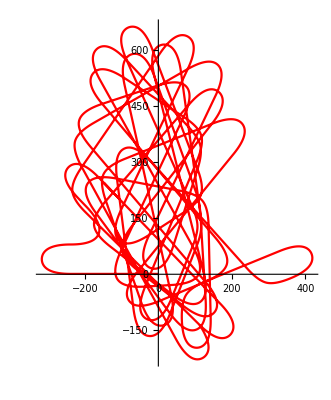

-Graphics3D-

```mathematica
g2=ListLinePlot[Table[{trajectory1[[i,1]],trajectory1[[i,3]]},{i,1,Length[trajectory1]}],PlotRange->All,AspectRatio->Automatic,PlotStyle->Red]

ListLinePlot3D[Table[{trajectory1[[i,1]],trajectory1[[i,2]],trajectory1[[i,3]]},{i,1,Length[trajectory1]}],PlotRange->All,BoxRatios->Automatic,PlotStyle->Red]
```

```mathematica
(*αst=π/36;
ϕst=1;

xst=20;
yst=1.5;
zst=1;*)

vlet[αst_,ϕst_,xst_,yst_,zst_]:=(
traj1=UpDownT[yst,αst,Hud,αgr];

trajup={};
For[j=1,j<=Length[traj1],j++,AppendTo[trajup,{xst+traj1[[j,1]]*Cos[ϕst],traj1[[j,2]],zst-traj1[[j,1]]*Sin[ϕst],ϕst,9999,traj1[[j,3]],traj1[[j,4]],If[traj1[[j,5]]=="P2","PU","U"]}]];
AppendTo[trajup,{trajup[[-1,1]]+Lgru*Cos[ϕst],Hud,trajup[[-1,3]]-Lgru*Sin[ϕst],ϕst,9999,0,9999,"P2"}];
Return[trajup];

);

(*
traj2=twopointT[trajup[[-1,1]],trajup[[-1,3]],2π-trajup[[-1,4]],trajectory1[[1,1]],trajectory1[[1,3]],2π-trajectory1[[1,4]],Lgru];
For[j=Length[traj2],j>=1,j--,PrependTo[trajectory1,{traj2[[j,1]],Hud,traj2[[j,2]],2π-traj2[[j,3]],If[-traj2[[j,4]]<1000,-traj2[[j,4]]],0,9999,traj2[[j,5]]}]];*)
```